# BE/CS 196a Lab 13 Construction of a DNA origami tile array that reconfigures from a sword to a rattlesnake

## Tile diagram generator

```mathematica
edgeColor=Table[Lighter[ColorData["FallColors"][i],j],{j,0,2/3,1/3},{i,0,1,1/3}]//Flatten;
```

```mathematica
directedangle[a_,b_]:=If[Sign@Det[{a,b}]≥0,VectorAngle[a,b],2Pi-VectorAngle[a,b]];
```

tileAbstract generates an abstract diagram of a square tile.
edge = {edge 1, edge 2, edge 3, edge 4}
   edge i = {x, y}
   x = edge identity number
   y = 0 (non-interactive), 1 (giving), or 2 (receiving)

Option pattern may be used to define a pattern on a square tile:
pattern→“((x1, y1), (x2, y2)) @ (cx, cy), ...”
(x1, y1) and (x2, y2) define the start and end points of a line. 
The bottom left, top left, top right and bottom right corners of the square are (0, 0), (0, 1), (1, 1) and (1, 0), respectively.
(cx, cy) defines the center of an arc, clockwise connecting the start point to the end point.
When @ is missing, the points are connected by a straight line.

Option customPattern may be used to define custom patterns given as a list of 2D graphics objects. 
Option LineThickness may be used to change the thickness of lines shown. The default thickness is 3. 
Option tilename may be used to display a name on the tile, given as a string. 
Option edgelabel→False may be used to remove any edge labels when the tile name is displayed.
option rotate may be used to rotate the tile without rotating the edge labels or tile name, given as a number of degrees.

```mathematica
Options[tileAbstract]={pattern->"",LineThickness->3,LabelSize->0.2,
tilename->"",edgelabel->True,rotate->0,customPattern->{}};
tileAbstract[edge_,OptionsPattern[]]:=Module[
{flatlist,list,i,pair,n,p1,p2,center,r,d1,d2,edgelabelpos},
flatlist=StringSplit[OptionValue[pattern],{"(",")",","," "}];
list={};
i=1;
While[i<=Length[flatlist],
pair={};
n=4;
While[i<Length[flatlist]&& StringLength[flatlist[[i]]]==0 ,i++];
If[StringLength[flatlist[[i]]]==0,Break[]];
While[Length[pair]<n || flatlist[[i]]=="@",
If[flatlist[[i]]=="@",n=6,
AppendTo[pair,ToExpression[flatlist[[i]]]]];
i++;
If[i>Length[flatlist],Break[]];
While[i<Length[flatlist] && StringLength[flatlist[[i]]]==0 ,i++]
];
AppendTo[list,pair]
];
Graphics[{
{White,Rectangle[{-0.1,-0.1},{1.1,1.1}]},
{Lighter[Gray,0.5],Rectangle[]},
Rotate[{
Table[{AbsoluteThickness[OptionValue[LineThickness]],If[Length[list[[i]]]==4,
Line[Partition[list[[i]],2]],
{p1,p2,center}=Partition[list[[i]],2];
r=EuclideanDistance[center,p1];
d1=directedangle[{1,0},p1-center];
d2=directedangle[{1,0},p2-center];
If[d1<d2,d2-=2Pi];
Circle[center,r,{d1,d2}]]},
{i,1,Length[list]}],
OptionValue[customPattern],
Switch[edge[[1,2]],
	0, {},
	1, {edgeColor[[edge[[1,1]]]],Polygon[{{0.4,0.9},{0.6,0.9},{0.5,1.1}}]},
	2, {{edgeColor[[edge[[1,1]]]],Polygon[{{0.4,1.05},{0.6,1.05},{0.5,0.85}}]},
		{White,Polygon[{{0.4,1.1},{0.6,1.1},{0.5,0.9}}]}},
	3, {Rectangle[{0.4,0.95},{0.6,1.05}]}],
Switch[edge[[2,2]],
	0, {},
	1, {edgeColor[[edge[[2,1]]]],Polygon[{{0.9,0.4},{0.9,0.6},{1.1,0.5}}]},
	2, {{edgeColor[[edge[[2,1]]]],Polygon[{{1.05,0.4},{1.05,0.6},{0.85,0.5}}]},
		{White,Polygon[{{1.1,0.4},{1.1,0.6},{0.9,0.5}}]}},
	3, {Rectangle[{0.95,0.4},{1.05,0.6}]}],
Switch[edge[[3,2]],
	0, {},
	1, {edgeColor[[edge[[3,1]]]],Polygon[{{0.4,0.1},{0.6,0.1},{0.5,-0.1}}]},
	2, {{edgeColor[[edge[[3,1]]]],Polygon[{{0.4,-0.05},{0.6,-0.05},{0.5,0.15}}]},
		{White,Polygon[{{0.4,-0.1},{0.6,-0.1},{0.5,0.1}}]}},
	3, {Rectangle[{0.4,-0.05},{0.6,0.05}]}],
Switch[edge[[4,2]],
	0, {},
	1, {edgeColor[[edge[[4,1]]]],Polygon[{{0.1,0.4},{0.1,0.6},{-0.1,0.5}}]},
	2, {{edgeColor[[edge[[4,1]]]],Polygon[{{-0.05,0.4},{-0.05,0.6},{0.15,0.5}}]},
		{White,Polygon[{{-0.1,0.4},{-0.1,0.6},{0.1,0.5}}]}},
	3, {Rectangle[{-0.05,0.4},{0.05,0.6}]}]},
OptionValue[rotate]Degree,{0.5,0.5}],	
If[OptionValue[tilename]!="",Text[Style[OptionValue[tilename],Black,FontSize->Scaled[OptionValue[LabelSize]],FontFamily->"Calibri"],{0.5,0.5}]],
edgelabelpos=RotateRight[{{0.5,0.75},{0.75,0.5},{0.5,0.25},{0.25,0.5}},OptionValue[rotate]/90];
If[OptionValue[edgelabel] && OptionValue[pattern]=="",
Table[If[edge[[i,1]]!=0,
Text[Style[Switch[edge[[i,2]],1,edge[[i,1]],2,SuperStar[edge[[i,1]]]],
Black,FontSize->Scaled[OptionValue[LabelSize]],FontFamily->"Calibri"],edgelabelpos[[i]]]],
{i,4}]]},
ImagePadding->0,PlotRangePadding->0,ImageMargins->0,ImageSize->100]];
```

## CRN Simulator

Chemical Reaction Network (CRN) Simulator package is developed by David Soloveichik. Copyright 2009-2015. 
http://users.ece.utexas.edu/~soloveichik/crnsimulator.html

### Public interface specification

```mathematica
Notation`AutoLoadNotationPalette = False;
Needs["Notation`"]
BeginPackage["CRNSimulator`", {"Notation`"}];
```

```mathematica
rxn::usage="Represents an irreversible reaction. eg. rxn[a+b,c,1]";
revrxn::usage="Represents a reversible reaction. eg. revrxn[a+b,c,1,1]";
conc::usage="Initial concentration: conc[x,10] or conc[{x,y},10].";
term::usage="Represents an additive term in the ODE for species x. \
Species concentrations must be expressed in x[t] form. eg. term[x, -2 x[t]*y[t]]";
```

```mathematica
SimulateRxnsys::usage=
"SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 \
to endtime. In rxnsys, initial concentrations are specified by conc statements. \
If no initial condition is set for a species, its initial concentration is set to 0. \
Rxnsys can also include term[] statements (e.g. term[x, -2 x[t]]) which are additively \
combined together with term[]s derived from rxn[] statements. \
Rxnsys can also include direct ODE definitions for some species (e.g. x'[t]==...), \
or direct definitions of species as functions of time (e.g. x[t]==...), \
which are passed to NDSolve without modification. \
Any options specified (eg WorkingPrecision->30) \
are passed to NDSolve."; 
SpeciesInRxnsys::usage=
"SpeciesInRxnsys[rxnsys] returns the species in reaction system rxnsys. \
SpeciesInRxnsys[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica pattern pttrn (eg x[1,_]).";
SpeciesInRxnsysStringPattern::usage=
"SpeciesInRxnsysPattern[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica string pattern pttrn. \
(Eg \"g$*\" matches all species names starting with \"g$\" ; \ 
can also do RegularExpression[\"o..d.\$.*\"].)";
RxnsysToOdesys::usage=
"RxnsysToOdesys[rxnsys,t] returns the ODEs corresponding to reaction system rxnsys, \
with initial conditions. If no initial condition is set for a species, its initial \
concentration is set to 0. \
The time variable is given as the second argument; if omitted it is set to Global`t.";
```

```mathematica
(*To use instead of Sequence in functions with Hold attribute but not HoldSequence,
like Module, If, etc*)
Seq:=Sequence
```

### Private

```mathematica
Begin["`Private`"];
```

```mathematica
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", OverscriptBox["→", RowBox[{" ", "k_", " "}]], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"rxn", "[", RowBox[{"r_", ",", "p_", ",", "k_"}], "]"}]]]
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", UnderoverscriptBox["⇄", "k2_", "k1_"], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"revrxn", "[", RowBox[{"r_", ",", "p_", ",", "k1_", ",", "k2_"}], "]"}]]]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", OverscriptBox["→", RowBox[{" ", "□", " "}]], " ", "□", " "}]],"rxn"]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", UnderoverscriptBox["⇄", "□", "□"], " ", "□", " "}]],"revrxn"]
```

```mathematica
(*We want rxn[a+b,c,1] to be different from rxn[b+a,c,1], so we have to set attribute
HoldAll. But we also want to evaluate if any variables can be evaluated.*)
SetAttributes[{rxn,revrxn}, HoldAll]
rxn[rs_Plus,ps_,k_]:=
 ReleaseHold[ReplacePart[rxn[1,ps,k],1->Hold[Plus]@@List@@Unevaluated[rs]]]/;
 Hold@@Unevaluated[rs] =!= Hold@@List@@Unevaluated[rs]
rxn[rs_,ps_Plus,k_]:=
 ReleaseHold[ReplacePart[rxn[rs,1,k],2->Hold[Plus]@@List@@Unevaluated[ps]]]/;
 Hold@@Unevaluated[ps] =!= Hold@@List@@Unevaluated[ps]
rxn[rs_,ps_,k_]:=
 (With[{rse=rs},rxn[rse,ps,k]])/;Head[rs]=!=Plus&&Unevaluated[rs]=!=rs
rxn[rs_,ps_,k_]:=
 (With[{pse=ps},rxn[rs,pse,k]])/;Head[ps]=!=Plus&&Unevaluated[ps]=!=ps
rxn[rs_,ps_,k_]:=
 (With[{ke=k},rxn[rs,ps,ke]])/;Unevaluated[k]=!=k
```

```mathematica
(* Automatically expand revrxn and concentration lists *)
revrxn[r_,p_,k1_,k2_]:=Sequence[rxn[r,p,k1],rxn[p,r,k2]]
conc[xs_List,c_]:=Seq@@(conc[#,c]&/@xs)

(* People are often confused about rxn[0,x,1] instead of rxn[1,x,1]. So we automatically replace any integer with 1. *)
rxn[Except[1,_Integer],ps_,k_]:=rxn[1,ps,k]
```

```mathematica
(* Species as products or reactants in rxn[] statements, as well as defined in x'[t]== or x[t]== statements \
or term statements, or conc statements *)
SpeciesInRxnsys[rxnsys_]:=
 Union[
 	Cases[Cases[rxnsys,rxn[r_,p_,_]:>Seq[r,p]]/.Times|Plus->Seq,s_Symbol|s_Symbol[__]],
 	Cases[rxnsys, x_'[_]==_ | x_[_]==_ | term[x_,__] | conc[x_,_] :> x]]
SpeciesInRxnsys[rsys_,pattern_]:=Cases[SpeciesInRxnsys[rsys],pattern]
SpeciesInRxnsysStringPattern[rsys_,pattern_]:=Select[SpeciesInRxnsys[rsys],StringMatchQ[ToString[#],pattern]&]
```

```mathematica
(* Check if a species' initial value is set in a odesys *) 	
InitialValueSetQ[odesys_,x_]:=
 MemberQ[odesys,x[_]==_]

(* Check if a species is missing an ODE or a direct definition (x[t]=_) in odesys. *)
MissingODEQ[odesys_,x_,t_Symbol]:=
 !MemberQ[odesys, D[x[t],t]==_ | x[t]==_]  	

RxnsysToOdesys[rxnsys_,t_Symbol:Global`t]:=
 Module[
  {spcs=SpeciesInRxnsys[rxnsys], concs, termssys, odesys, eqsFromTerms, eqsFromConcs},

  (* extract conc statements and sum them for same species *)
  concs = conc[#[[1,1]],Total[#[[;;,2]]]]&/@GatherBy[Cases[rxnsys,conc[__]],Extract[{1}]];

  (* Convert rxn[] to term[] statements *)
  termssys=rxnsys /. rxn:rxn[__]:>Seq@@ProcessRxnToTerms[rxn,t];

  (* ODEs from parsing terms *)
  eqsFromTerms = ProcessTermsToOdes[Cases[termssys,term[__]],t]; 
  (* initial values from parsing conc statements *)
  eqsFromConcs = Cases[concs,conc[x_,c_]:>x[0]==c]; 

  (* Remove term and conc statements from rxnsys and add eqs generated from them. 
     If there is a conflict, use pass-through equations *)
  odesys = DeleteCases[termssys, term[__]|conc[__]];
  odesys = Join[odesys,
                DeleteCases[eqsFromTerms, Alternatives@@(#'[t]==_& /@ Cases[odesys,(x_'[t]|x_[t])==_:>x])],
                eqsFromConcs];
     
  (* For species still without initial values, add zeros *)
  odesys = Join[odesys, #[0]==0& /@ Select[spcs, !InitialValueSetQ[odesys,#]&]];

  (* For species still without ODE or direct definition, add zero time derivative *)
  (* This can happen for example if conc is defined, but nothing else *)
  Join[odesys, D[#[t],t]==0& /@ Select[spcs, MissingODEQ[odesys,#,t]&]]
 ]
 
(* Create list of ODEs from parsing term statements. terms should be list of term[] statements. *) 
ProcessTermsToOdes[terms_,t_Symbol]:=
Module[{spcs=Union[Cases[terms,term[s_,_]:>s]]},
#'[t]==Total[Cases[terms,term[#,rate_]:>rate]] & /@ spcs];

(* Create list of term[] statements from parsing a rxn statement *) 
ProcessRxnToTerms[reaction:rxn[r_,p_,k_],t_Symbol]:=
Module[{spcs=SpeciesInRxnsys[{reaction}], rrate, spccoeffs,terms},
(* compute rate of this reaction *)
rrate = k (r/.{Times[b_,s_]:>s^b,Plus->Times});
(*for each species, get a net coefficient*)
spccoeffs=Coefficient[p-r,#]& /@ spcs;
(*create term for each species*)
terms=MapThread[term[#1,#2*rrate]&,{spcs, spccoeffs}];
(*change all species variables in the second arg in term[] to be functions of t*)
terms/.term[spc_,rate_]:>term[spc,rate/.s_/;MemberQ[spcs,s]:>s[t]]];
```

```mathematica
SimulateRxnsys[rxnsys_,endtime_,opts:OptionsPattern[NDSolve]]:=
 Module[{spcs=SpeciesInRxnsys[rxnsys],odesys=RxnsysToOdesys[rxnsys,Global`t]},
 Quiet[NDSolve[odesys, spcs, {Global`t,0,endtime},opts,MaxSteps->Infinity,AccuracyGoal->MachinePrecision],{NDSolve::"precw"}][[1]]]
```

```mathematica
End[];
EndPackage[];
```

## Polymer CRNs

listToSpeciesName converts a polymer stored as a list of monomers to a species name that joins all monomers.

```mathematica
listToSpeciesName[list_]:=ToExpression[StringJoin[Table[ToString[list[[i]]],{i,Length[list]}]]]
```

polymerCRN generates a list of polymers and a list of polymer reactions based on a list of monomers, a list of rules for how the monomers interact with each other (each rule is defined as a pair of monomers with an order that applies to all rules, e.g. left to right, bottom to top), a list of rates of monomer interactions (one for each rule), and the maximum length of polymers enumerated (maxlength). 

Note: An experimental system will not have a set maximum length of polymers, and polymers could grow infinitely (whether it is likely or not depends on parameters including concentrations and rates). Setting a maximum length in simulation allows for the approximate modeling of an infinite chemical reaction network. The choice of the maximum length will affect the result of simulation (i.e. how accurate the approximation is). To understand the expected behavior of an experimental system, a good choice of the maximum length is just large enough so that no significant change in the result is observed with a larger number.

```mathematica
polymerCRN[monomers_,rules_,rates_,maxlength_]:=Module[{polymers,rxnsys,n1,n2,m,i,j,k,p,q,ruleset,newpolymer,newrxn},
polymers=Table[{{monomers[[i]]}},{i,Length[monomers]}];
rxnsys={};
n1=0;n2=0;m=1;
While[n1<n2 || m==1,
n1=n2;m++;
For[i=1,i≤Length[polymers],i++,
For[j=1,j≤Length[polymers[[i]]],j++,
ruleset=Position[rules[[;;,1]],polymers[[i,j,-1]]];
For[k=1,k≤Length[ruleset],k++,
p=Position[polymers[[;;,1,1]],rules[[ruleset[[k,1]],2]]][[1,1]];
For[q=1,q≤Length[polymers[[p]]],q++,
newpolymer=Join[polymers[[i,j]],polymers[[p,q]]];
newrxn=rxn[listToSpeciesName[polymers[[i,j]]]+listToSpeciesName[polymers[[p,q]]],listToSpeciesName[newpolymer],rates[[ruleset[[k,1]]]]];
If[FreeQ[polymers[[i]],newpolymer] && Length[newpolymer]≤maxlength,AppendTo[polymers[[i]],newpolymer]];
If[FreeQ[rxnsys,newrxn] && Length[newpolymer]≤maxlength,AppendTo[rxnsys,newrxn];
n2++]
]]]]];
{Table[listToSpeciesName[polymers[[i,j]]],{i,Length[polymers]},{j,Length[polymers[[i]]]}]//Flatten,
rxnsys}]
```

## Plot function

PlotSim function plots a simulation including multiple trajectories.
SIMcircuit is a simulation.
SIMtime is the simulation time.  
trajectories is a list of species names or concentrations shown in the legend. The default is none.
TrajectoryLabel is a label for the legend of trajectories. The default is none.
OutputLabel is a label for the vertical axis, which should be a description of the output simulated, with unit specified. The default is none.
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range. The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit is nM. Same format and default as timeRange.

```mathematica
Options[PlotSim]={plotSize->300,labelSize->16,lineThickness->2};
PlotSim[SIMcircuit_,SIMtime_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All,OptionsPattern[]]:=Module[{colors},
colors=Table[ColorData["Rainbow"][i],{i,If[Length[SIMcircuit]<8,0.12,0],0.96,0.96/Length[SIMcircuit]}];
Plot[SIMcircuit,{t,0,SIMtime},PlotLabel->Style[CircuitLabel,OptionValue[labelSize]],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->{{AbsoluteThickness[OptionValue[lineThickness]],#}&/@colors}[[1]],
PlotLegends->Placed[SwatchLegend[colors,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->OptionValue[labelSize]*0.75],Right],
LabelStyle->Directive[Gray,FontSize->OptionValue[labelSize],FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->OptionValue[plotSize]]]
```

## Diagrams of tiles and tile arrays

### Sword diagrams

Tiles with edge labels

```mathematica
S1E=tileAbstract[{{1,1},{1,1},{1,1},{4,1}},rotate->180]
```

-Graphics-

```mathematica
BTE=tileAbstract[{{0,0},{2,2},{0,0},{4,2}}]
```

-Graphics-

```mathematica
S2E=tileAbstract[{{1,1},{0,0},{2,1},{0,0}},rotate->-90]
```

-Graphics-

```mathematica
S3E=tileAbstract[{{1,2},{0,0},{0,0},{0,0}},rotate->90]
```

-Graphics-

Tile arrays with edge labels

```mathematica
swordArrayEdge=Grid[{
{"",Rotate[S3E,90Degree]},
{Rotate[S3E,180Degree],S1E,BTE,S2E,S3E},
{"",Rotate[S3E,-90Degree]}},
Spacings->{0,0}]
```

| -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- |  |  |

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordArrayEdge.png",swordArrayEdge];
```

Tiles with names

```mathematica
S1N=tileAbstract[{{1,1},{1,1},{1,1},{4,1}},rotate->180,tilename->"S1",LabelSize->0.4,edgelabel->False]
```

-Graphics-

```mathematica
BTN=tileAbstract[{{0,0},{2,2},{0,0},{4,2}},tilename->"BT",LabelSize->0.4,edgelabel->False]
```

-Graphics-

```mathematica
S2N=tileAbstract[{{1,1},{0,0},{2,1},{0,0}},rotate->-90,tilename->"S2",LabelSize->0.4,edgelabel->False]
```

-Graphics-

```mathematica
S3N=tileAbstract[{{1,2},{0,0},{0,0},{0,0}},rotate->90,tilename->"S3",LabelSize->0.4,edgelabel->False]
```

-Graphics-

Tile arrays with edge labels

```mathematica
swordArrayName=Grid[{
{"",Rotate[S3N,90Degree]},
{Rotate[S3N,180Degree],S1N,BTN,S2N,S3N},
{"",Rotate[S3N,-90Degree]}},
Spacings->{0,0}]
```

| -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- |  |  |

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordArrayName.png",swordArrayName];
```

Tiles with patterns

```mathematica
aster=tileAbstract[ConstantArray[{0,0},4],
pattern->"((0,2/3),(2/3,0))@(0,0),((1/3,0),(1,2/3))@(1,0),((1,1/3),(1/3,1))@(1,1),((2/3,1),(0,1/3))@(0,1)",
LineThickness->5]
```

-Graphics-

```mathematica
line=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Rectangle[{0,1/3},{1,2/3}]}]
```

-Graphics-

```mathematica
point=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Polygon[{{0,1/3},{1/3,1/3},{3/4,1/2},{1/3,2/3},{0,2/3}}]}]
```

-Graphics-

Tile arrays with patterns

```mathematica
swordArrayPattern=Grid[{
{"",Rotate[point,90 Degree]},
{Rotate[point,180 Degree],aster,line,line,point},
{"",Rotate[point,-90 Degree]}},
Spacings->{0,0}]
```

| -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- |  |  |

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordArrayPattern.png",swordArrayPattern];
```

### Snake tail invader diagrams

Tiles with edge labels

```mathematica
aTileE=tileAbstract[{{1,1},{2,1},{0,0},{0,0}},rotate->-90]
```

-Graphics-

```mathematica
bTileE=tileAbstract[{{1,2},{2,2},{0,0},{0,0}},rotate->90]
```

-Graphics-

```mathematica
cTileE=tileAbstract[{{1,2},{0,0},{0,0},{0,0}},rotate->90]
```

-Graphics-

Tile arrays with edge labels

```mathematica
abacArrayEdge=Grid[{
{"",aTileE,cTileE},
{aTileE,bTileE}},
Spacings->{0,0}]
```

| -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
snaketailArrayEdge=Table[Grid[
Join[{{ConstantArray["",x],aTileE,cTileE}//Flatten},
Table[{ConstantArray["",y],aTileE,bTileE}//Flatten,{y,x-1,0,-1}]],
Spacings->{0,0}],{x,0,4}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
For[i=1,i≤5,i++,
Export["snaketailArrayEdge_"<>ToString[i]<>".png",snaketailArrayEdge[[i]]]
];
```

Tiles with names

```mathematica
aTileN=tileAbstract[{{1,1},{2,1},{0,0},{0,0}},rotate->-90,tilename->"a",edgelabel->False,LabelSize->0.4]
```

-Graphics-

```mathematica
bTileN=tileAbstract[{{1,2},{2,2},{0,0},{0,0}},rotate->90,tilename->"b",edgelabel->False,LabelSize->0.4]
```

-Graphics-

```mathematica
cTileN=tileAbstract[{{1,2},{0,0},{0,0},{0,0}},rotate->90,tilename->"c",edgelabel->False,LabelSize->0.4]
```

-Graphics-

Tile arrays with names

```mathematica
abacArrayName=Grid[{
{"",aTileN,cTileN},
{aTileN,bTileN}},
Spacings->{0,0}]
```

| -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
snaketailArrayName=Table[Grid[
Join[{{ConstantArray["",x],aTileN,cTileN}//Flatten},
Table[{ConstantArray["",y],aTileN,bTileN}//Flatten,{y,x-1,0,-1}]],
Spacings->{0,0}],{x,0,4}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
For[i=1,i≤5,i++,
Export["snaketailArrayName_"<>ToString[i]<>".png",snaketailArrayName[[i]]]
];
```

Tiles with patterns

```mathematica
arc=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{1,0},{1/3,2/3},{Pi/2,Pi}]}]
```

-Graphics-

```mathematica
line=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Rectangle[{0,1/3},{1,2/3}]}]
```

-Graphics-

Tile arrays with patterns

```mathematica
abacArrayPattern=Grid[{
{"",arc,line},
{arc,Rotate[arc,180Degree]}},
Spacings->{0,0}]
```

| -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
snaketailArrayPattern=Table[Grid[
Join[{{ConstantArray["",x],arc,line}//Flatten},
Table[{ConstantArray["",y],arc,Rotate[arc,180Degree]}//Flatten,{y,x-1,0,-1}]],
Spacings->{0,0}],{x,0,4}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
For[i=1,i≤5,i++,
Export["snaketailArrayPattern_"<>ToString[i]<>".png",snaketailArrayPattern[[i]]]
];
```

### Snake head invader diagrams

Tiles with edge labels

```mathematica
H1E=tileAbstract[{{4,1},{0,0},{1,1},{2,1}}]
```

-Graphics-

```mathematica
H2E=tileAbstract[{{1,2},{0,0},{0,0},{4,2}}]
```

-Graphics-

```mathematica
H3E=tileAbstract[{{3,1},{4,1},{0,0},{0,0}}]
```

-Graphics-

```mathematica
H4E=tileAbstract[{{0,0},{2,2},{3,2},{0,0}}]
```

-Graphics-

Tile arrays with edge labels

```mathematica
snakeheadArrayEdge=Grid[{
{H4E,H1E},
{H3E,H2E}},
Spacings->{0,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snakeheadArrayEdge.png",snakeheadArrayEdge];
```

Tiles with patterns

```mathematica
H1p=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{0,1},{5/18,7/18},{-Pi/2,0}],
Polygon[{{10/18,0.8},{11/18,1},{13/18,1},{12/18,0.8}}],
Rectangle[{10/18,0.2},{12/18,0.8}],
Polygon[{{10/18,0.2},{11/18,0},{13/18,0},{12/18,0.2}}],
Disk[{0.15,0.35},0.06],Disk[{0.35,0.15},0.06]}]
```

-Graphics-

```mathematica
H2p=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{0,1},{11/18,13/18},{-Pi/2,0}],Disk[{0.75,0.35},0.06]}]
```

-Graphics-

```mathematica
H3p=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{1,1},{11/18,13/18},{Pi,3Pi/2}],Disk[{0.1,0.7},0.06]}]
```

-Graphics-

```mathematica
H4p=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{1,0},{11/18,13/18},{Pi/2,Pi}],Disk[{0.2,0.9},0.06]}]
```

-Graphics-

Tile arrays with patterns

```mathematica
snakeheadArrayPatten=Grid[{
{H4p,H1p},
{H3p,H2p}},
Spacings->{0,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snakeheadArrayPatten.png",snakeheadArrayPatten];
```

Tiles with names

```mathematica
H1N=tileAbstract[{{4,1},{0,0},{1,1},{2,1}},tilename->"H1",LabelSize->0.4,edgelabel->False]
```

-Graphics-

```mathematica
H2N=tileAbstract[{{1,2},{0,0},{0,0},{4,2}},tilename->"H2",LabelSize->0.4,edgelabel->False]
```

-Graphics-

```mathematica
H3N=tileAbstract[{{3,1},{4,1},{0,0},{0,0}},tilename->"H3",LabelSize->0.4,edgelabel->False]
```

-Graphics-

```mathematica
H4N=tileAbstract[{{0,0},{2,2},{3,2},{0,0}},tilename->"H4",LabelSize->0.4,edgelabel->False]
```

-Graphics-

Tile arrays with names

```mathematica
snakeheadArrayName=Grid[{
{H4N,H1N},
{H3N,H2N}},
Spacings->{0,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snakeheadArrayName.png",snakeheadArrayName];
```

### Sword with snake tail

```mathematica
swordtailArray=Grid[{
{"",Rotate[S3N,90 Degree]},
{Rotate[S3N,180 Degree],S1N,BTN,Rotate[aTileN,-90Degree]},
{"",Rotate[S3N,-90 Degree],"",Rotate[bTileN,-90Degree],Rotate[aTileN,-90Degree]},
{"","","","",Rotate[cTileN,-90Degree]}},
Spacings->{0,0}]
```

| -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 | -Graphics- |  | -Graphics- | -Graphics-
 |  |  |  | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordtailArray.png",swordtailArray];
```

```mathematica
swordtailPattern=Grid[{
{"",Rotate[point,90 Degree]},
{Rotate[point,180 Degree],aster,line,Rotate[arc,-90Degree]},
{"",Rotate[point,-90 Degree],"",Rotate[arc,90Degree],Rotate[arc,-90Degree]},
{"","","","",Rotate[line,90Degree]}},
Spacings->{0,0}]
```

| -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 | -Graphics- |  | -Graphics- | -Graphics-
 |  |  |  | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordtailPattern.png",swordtailPattern];
```

### Sword with snake head

```mathematica
swordheadPatten=Grid[{
{Rotate[H3p,-90Degree],Rotate[H4p,-90Degree]},
{Rotate[H2p,-90Degree],Rotate[H1p,-90Degree],line,line,point}},
Spacings->{0,0}]
```

-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordheadPatten.png",swordheadPatten];
```

```mathematica
swordheadArray=Grid[{
{Rotate[H3N,-90Degree],Rotate[H4N,-90Degree]},
{Rotate[H2N,-90Degree],Rotate[H1N,-90Degree],BTN,S2N,S3N}},
Spacings->{0,0}]
```

-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordheadArray.png",swordheadArray];
```

### Sword with snake head and tail

```mathematica
swordheadtailPatten=Grid[{
{Rotate[H3p,-90Degree],Rotate[H4p,-90Degree]},
{Rotate[H2p,-90Degree],Rotate[H1p,-90Degree],line,Rotate[arc,-90Degree]},
{"","","",Rotate[arc,90Degree],Rotate[arc,-90Degree]},
{"","","","",Rotate[line,90Degree]}},
Spacings->{0,0}]
```

-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 |  |  | -Graphics- | -Graphics-
 |  |  |  | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordheadtailPatten.png",swordheadtailPatten];
```

```mathematica
swordheadtailArray=Grid[{
{Rotate[H3N,-90Degree],Rotate[H4N,-90Degree]},
{Rotate[H2N,-90Degree],Rotate[H1N,-90Degree],BTN,Rotate[aTileN,-90Degree]},
{"","","",Rotate[bTileN,-90Degree],Rotate[aTileN,-90Degree]},
{"","","","",Rotate[cTileN,-90Degree]}},
Spacings->{0,0}]
```

-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 |  |  | -Graphics- | -Graphics-
 |  |  |  | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["swordheadtailArray.png",swordheadtailArray];
```

## Sword array experiment-veronica

In the example AFM image below, one expected and one unexpected structure are highlighted, with an interpretation of each structure based on its shape and pattern. Note: It is often not straightforward to interpret structures in AFM images, especially the unexpected ones, because the patterns may have certain symmetries or otherwise appear ambiguous, the structures in the AFM images may landed right-side-up or upside-down on mica, and besides the designed interactions tiles may interact with each other through spurious interactions.

Study the AFM images of the sword array and discover the characters of the molecular structures. You may use the highlighted example structures as a starting point, but don’t let that limit your own observations. Come up with a hypothesis about what might have affected the yield of the desired structures, propose control/debugging experiments that could either verify or refute your hypothesis, and discuss possible changes in the design or experimental procedure that could improve the yield.

-Graphics-

From the group presentation: Veronica’s part
The most common error among this sample was a missing “hilt” piece, from one side of the array.
Because the location of the error is consistent, it is more likely due to unexpected molecular behavior than experimental error.
The cause of this error is likely weak edge interactions between the S1 and S3 tiles. 
We can test this using a 1:3 mixture of S1 and S3 tiles only.

## Snake tail invader, experiment 1 (a:b:c=2:1:1)-aditi

Use polymerCRN defined above to enumerate polymer reactions given a set of monomers and their interactions.

```mathematica
monomers={a,b,c};
rules={{a,b},{a,c},{b,a}};
k=2*10^6;
rates={k,k,k};
maxlength=20;
{polymers,rxnsys}=polymerCRN[monomers,rules,rates,maxlength];
```

Simulate the polymer reactions given initial concentrations of the monomers.

```mathematica
SIMtime=2; (* unit: hours *)
sc=10*10^-9; (* standard concentration, unit: M *)
polymersys={
rxnsys,
conc[a,2*sc],
conc[b,1*sc],
conc[c,1*sc]
}//Flatten;
sol=SimulateRxnsys[polymersys,SIMtime*60*60];
SIMpolymer=Table[polymers[[i]][t*60*60]/10^-9/.sol,{i,Length[polymers]}];
```

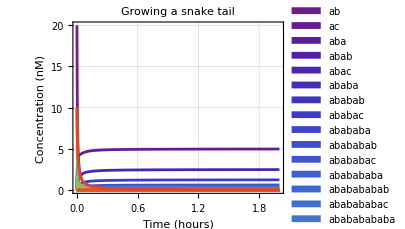

```mathematica
trajectories=polymers;
TrajectoryLabel="";
OutputLabel="Concentration (nM)"; 
CircuitLabel="Growing a snake tail";  
TimeRange={All,1};
PlotSim[SIMpolymer,SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel,TimeRange]
```

Display final concentrations of polymers above a set threshold.

```mathematica
SIMpolymerFinal=Table[polymers[[i]][SIMtime*60*60]/10^-9/.sol,{i,Length[polymers]}];
threshold=0.2; (* threshold concentration, unit: nM *)
polymerThresholded=Position[SIMpolymerFinal,x_/;x>=threshold]//Flatten;
```

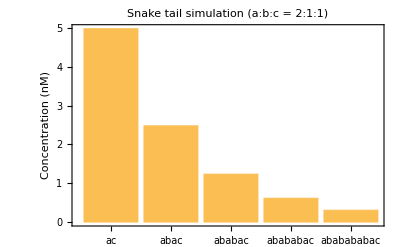

```mathematica
snaketailSim1=BarChart[SIMpolymerFinal[[polymerThresholded]],ChartLabels->Placed[polymers[[polymerThresholded]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Concentration (nM)",16],LabelStyle->16,
PlotLabel->"Snake tail simulation (a:b:c = 2:1:1)"]
```

Counts of the above polymers in AFM images.

```mathematica
polymersExp1={{ac,58},{abac,15},{ababac,5},{abababac,0},{ababababac,1}};
```

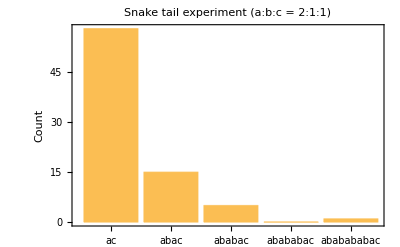

```mathematica
snaketailExp1=BarChart[polymersExp1[[;;,2]],
ChartLabels->Placed[polymersExp1[[;;,1]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Count",16],LabelStyle->16,
PlotLabel->"Snake tail experiment (a:b:c = 2:1:1)"]
```

Display simulation and experimental result together, polymer concentrations and counts are now shown as fractions.

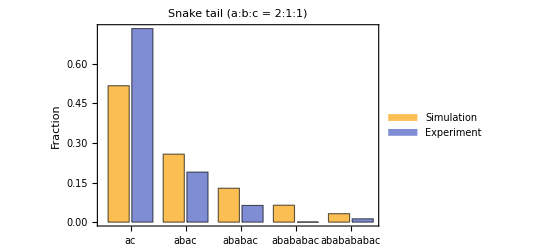

```mathematica
snaketailSimExp1=BarChart[MapThread[{#1/Total[SIMpolymerFinal[[polymerThresholded]]],#2/Total[polymersExp1[[;;,2]]]}&,{SIMpolymerFinal[[polymerThresholded]],polymersExp1[[;;,2]]}],
ChartLabels->{Placed[polymersExp1[[;;,1]],Axis,Rotate[#,Pi/4]&],None},
ChartLegends->{"Simulation","Experiment"},
Frame->True,FrameLabel->Style["Fraction",16],LabelStyle->16,
PlotLabel->"Snake tail (a:b:c = 2:1:1)"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snaketailSimExp1.png",snaketailSimExp1];
```

Now let’s look at a longer list of representative polymers in AFM images, given their interpretations and counts. Note that only one of all possible interpretations is given for each structure, with no particular emphasis on its likelihood. For example, “a” could also be “b”, and “ab” could also be “ba” or even “aa” or “bb” if spurious interactions exist.

It is clear that many of these polymers are not expected in the original simulation.

```mathematica
polymersExp1All={{a,15},{ab,15},{ac,58},{aab,2},{aba,8},{abab,5},{abac,15},{ababa,1},{ababab,3},{ababac,5},{abababa,2},{ababababac,1},{bac,5},{baac,1},{babac,1},{c,2},{cac,2},{cabac,3},{cababac,2}};
```

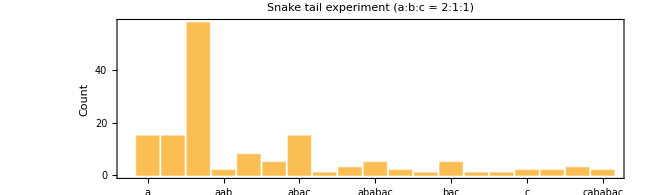

```mathematica
snaketailExp1All=BarChart[polymersExp1All[[;;,2]],
ChartLabels->Placed[polymersExp1All[[;;,1]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Count",16],LabelStyle->12,
PlotLabel->"Snake tail experiment (a:b:c = 2:1:1)",
AspectRatio->0.3,ImageSize->650]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snaketailExp1All.png",snaketailExp1All];
```

To better understand the experimental results, let’s explore a hypothesis about spurious interaction between edge 2 and 1*.

```mathematica
aTileE=tileAbstract[{{1,1},{2,1},{0,0},{0,0}}];
cTileE=tileAbstract[{{1,2},{0,0},{0,0},{0,0}},rotate->90];
caArrayEdge=Grid[{{aTileE,cTileE}},Spacings->{0,0}]
```

-Graphics- | -Graphics-

```mathematica
aTileN=tileAbstract[{{1,1},{2,1},{0,0},{0,0}},tilename->"a",edgelabel->False,LabelSize->0.4];
cTileN=tileAbstract[{{1,2},{0,0},{0,0},{0,0}},rotate->90,tilename->"c",edgelabel->False,LabelSize->0.4];
caArrayName=Grid[{{aTileN,cTileN}},Spacings->{0,0}]
```

-Graphics- | -Graphics-

Simulate the spurious interaction between edge 2 and 1*.

```mathematica
monomers={a,b,c,c1};   (* create c1 as a spurious version of c to enumerate the reactions and replace all c1 with c after the enumeration *)
rules={{a,b},{a,c},{b,a},{c1,a}};
k=2*10^6;
rates={k,k,k,k/5}; (* set the spurious reaction to be 5 times slower than the desired reactions *)
maxlength=20;
{polymers,rxnsys}=polymerCRN[monomers,rules,rates,maxlength];
polymers=ToExpression/@StringReplace[ToString/@polymers,"c1"->"c"]//DeleteDuplicates;
rxnsys=ToExpression/@StringReplace[ToString/@rxnsys,"c1"->"c"]//DeleteDuplicates;
```

```mathematica
SIMtime=2; (* unit: hours *)
sc=10*10^-9; (* standard concentration, unit: M *)
polymersys={
rxnsys,
conc[a,2*sc],
conc[b,1*sc],
conc[c,1*sc]
}//Flatten;
sol=SimulateRxnsys[polymersys,SIMtime*60*60];
SIMpolymer=Table[polymers[[i]][t*60*60]/10^-9/.sol,{i,Length[polymers]}];
```

Display final concentrations of polymers above a set threshold.

```mathematica
SIMpolymerFinal=Table[polymers[[i]][SIMtime*60*60]/10^-9/.sol,{i,Length[polymers]}];
threshold=0.2; (* threshold concentration, unit: nM *)
polymerThresholded=Position[SIMpolymerFinal,x_/;x>=threshold]//Flatten;
```

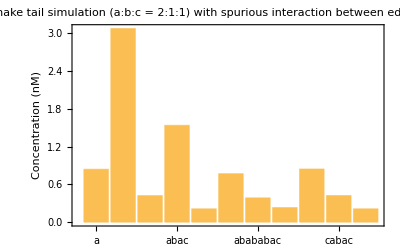

```mathematica
BarChart[SIMpolymerFinal[[polymerThresholded]],ChartLabels->Placed[polymers[[polymerThresholded]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Concentration (nM)",16],LabelStyle->14,
PlotLabel->"Snake tail simulation (a:b:c = 2:1:1)\n with spurious interaction between edge 2 and 1*",
ImageSize->400]
```

Find the above polymers in the list of representative polymers in AFM images. If any polymer is not found, add it to the list with count = 0.

```mathematica
For[i=1,i≤Length[polymerThresholded],i++,
If[FreeQ[polymersExp1All[[;;,1]],polymers[[polymerThresholded[[i]]]]],
AppendTo[polymersExp1All,{polymers[[polymerThresholded[[i]]]],0}]]];
```

```mathematica
polymerSelected=Position[polymersExp1All[[;;,1]],#]&/@polymers[[polymerThresholded]]//Flatten;
```

Display simulation and experimental result together, polymer concentrations and counts are now shown as fractions. The hypothesis of spurious interaction between edge 2 and 1* does explain some populations of polymers in the experimental results.

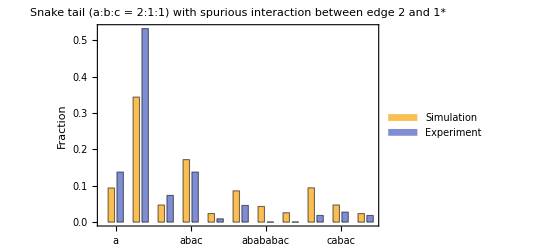

```mathematica
snaketailSimExp1Spurious1=BarChart[MapThread[{#1/Total[SIMpolymerFinal[[polymerThresholded]]],#2/Total[polymersExp1All[[polymerSelected,2]]]}&,{SIMpolymerFinal[[polymerThresholded]],polymersExp1All[[polymerSelected,2]]}],
ChartLabels->{Placed[polymersExp1All[[polymerSelected,1]],Axis,Rotate[#,Pi/4]&],None},
ChartLegends->{"Simulation","Experiment"},
Frame->True,FrameLabel->Style["Fraction",16],LabelStyle->14,
PlotLabel->"Snake tail (a:b:c = 2:1:1)\n with spurious interaction between edge 2 and 1*",
ImageSize->400]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snaketailSimExp1Spurious1.png",snaketailSimExp1Spurious1];
```

Let’s now look at the representative polymers in AFM images that are not displayed above -- they are still unexpected in the revised simulation including the hypothesized spurious interaction.

```mathematica
For[i=1,i≤Length[polymersExp1All],i++,
If[FreeQ[polymers[[polymerThresholded]],polymersExp1All[[i,1]]],
Print[polymersExp1All[[i]]]]];
```

{ab,15}

{aab,2}

{abab,5}

{ababab,3}

{abababa,2}

{ababababac,1}

{bac,5}

{baac,1}

{babac,1}

{c,2}

We can also look at the kinetics trajectories of some of these polymers: according to simulation, their concentrations should increase but then decrease over time as they are consumed in growing longer polymers. So either there are yet other aspects of the model that do not fully capture what happened in the experiment, or the interpretation of the polymers are incorrect, or both.

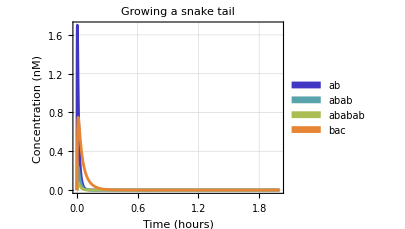

```mathematica
polymer={ab,abab,ababab,bac};
pos=Position[polymers,#]&/@polymer//Flatten;
trajectories=polymer;
TrajectoryLabel="";
OutputLabel="Concentration (nM)"; 
CircuitLabel="Growing a snake tail";   
TimeRange={All,1};
PlotSim[SIMpolymer[[pos]],SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel,TimeRange]
```

Continue with the second experiment and then explore other hypotheses that could explain more differences between the experimental results and simulation.

From the group presentation: Aditi’s part
Higher concentration of the shortest invader, lower concentrations of longer invaders, second longest structure was not observed
Preference for shorter structures might come from stronger interactions between a and c (check edges 1 and 1*) or weaker interactions between a and b (check edges 1, 2 and 1*, 2*)
Missing fourth structure might be from experimental errors or low concentration of b, try increasing relative concentration
Additional representative polymers not expected in the original simulation, highest concentration of expected invader (ac), unexpected structures in lower amounts, but still nonzero, explore hypothesis about spurious interactions between a and c
Possible spurious interactions between tiles a and c (edges 2 and 1*), does not explain the differences in experimental results, multiple factors (including spurious interactions), or these interactions aren’t occurring at all
Kinetic trajectories, according to simulation concentration should increase and then decrease, experimentally the concentrations of short structures were higher than expected, the model does not fully capture the experiment or polymer interpretation is wrong
Hypotheses, a is binding more selectively to c than b due to unexpected edge structure, experimental errors caused the difference in experimental concentrations (e.g. abscence of the abababac structure), spurious interactions between edges 2 and  1* may also be occurring
Debugging, increase concentration of b relative to c, decrease concentration of c relative to b, compare 1* receiving edges in b and c, test formation with only a and b tiles, see whether longer structures form at higher amounts

## Snake tail invader, experiment 2 (a:b:c=3:2:1)

Use polymerCRN defined above to enumerate polymer reactions given a set of monomers and their interactions.

```mathematica
monomers={a,b,c};
rules={{a,b},{a,c},{b,a}};
k=2*10^6;
rates={k/5,k*2,k/5};
maxlength=20;
{polymers,rxnsys}=polymerCRN[monomers,rules,rates,maxlength];
```

Simulate the polymer reactions given initial concentrations of the monomers.

```mathematica
SIMtime=2; (* unit: hours *)
sc=8*10^-9; (* standard concentration, unit: M *)
polymersys={
rxnsys,
conc[a,3*sc],
conc[b,2*sc],
conc[c,1*sc]
}//Flatten;
sol=SimulateRxnsys[polymersys,SIMtime*60*60];
SIMpolymer=Table[polymers[[i]][t*60*60]/10^-9/.sol,{i,Length[polymers]}];
```

Display final concentrations of polymers above a set threshold.

```mathematica
SIMpolymerFinal=Table[polymers[[i]][SIMtime*60*60]/10^-9/.sol,{i,Length[polymers]}];
threshold=0.5; (* threshold concentration, unit: nM *)
polymerThresholded=Position[SIMpolymerFinal,x_/;x>=threshold]//Flatten;
```

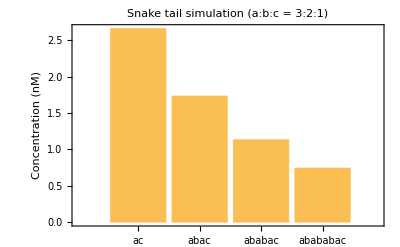

```mathematica
snaketailSim2=BarChart[SIMpolymerFinal[[polymerThresholded]],ChartLabels->Placed[
polymers[[polymerThresholded]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Concentration (nM)",16],LabelStyle->16,
PlotLabel->"Snake tail simulation (a:b:c = 3:2:1)"]
```

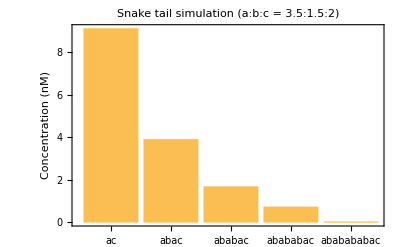

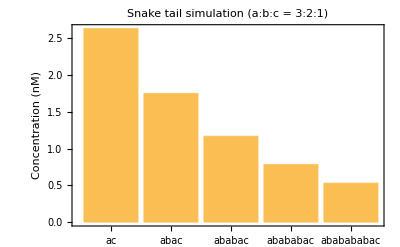

```mathematica
Insert[SIMpolymerFinal[[polymerThresholded]],0,-1]
Insert[polymers[[polymerThresholded]],"ababababac",-1]
```

The above polymers were counted in two AFM images, one image is shown below, and counts from both images are given below.

-Graphics-

```mathematica
polymersExp2Image1={{ac,36},{abac,16},{ababac,6},{abababac,1},{ababababac,0}};
polymersExp2Image2={{ac,23},{abac,13},{ababac,5},{abababac,5},{ababababac,0}};
polymersExp2=MapThread[{#1[[1]],#1[[2]]+#2[[2]]}&,{polymersExp2Image1,polymersExp2Image2}];
```

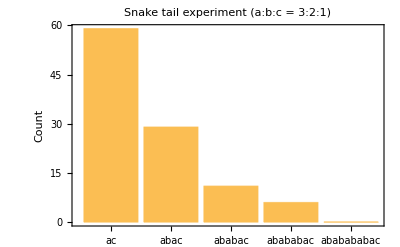

```mathematica
snaketailExp2=BarChart[polymersExp2[[;;,2]],
ChartLabels->Placed[polymersExp1[[;;,1]],Axis,Rotate[#,Pi/4]&],
Frame->True,FrameLabel->Style["Count",16],LabelStyle->16,
PlotLabel->"Snake tail experiment (a:b:c = 3:2:1)"]
```

Display simulation and experimental result together, polymer concentrations and counts are now shown as fractions.

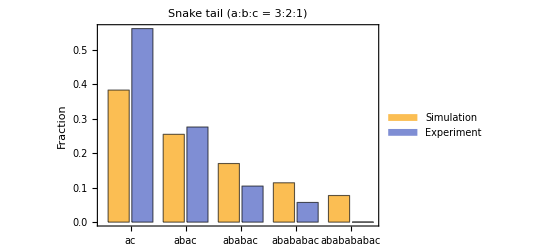

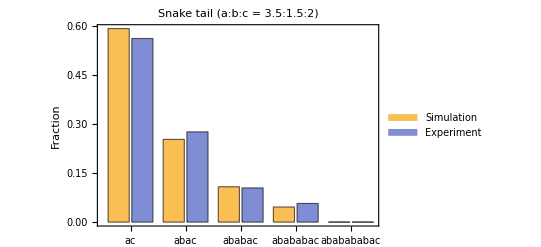

-Graphics-

-Graphics-

```mathematica
snaketailSimExp2=BarChart[MapThread[{#1/Total[SIMpolymerFinal[[polymerThresholded]]],#2/Total[polymersExp2[[;;,2]]]}&,{SIMpolymerFinal[[polymerThresholded]],polymersExp2[[;;,2]]}],
ChartLabels->{Placed[polymersExp2[[;;,1]],Axis,Rotate[#,Pi/4]&],None},
ChartLegends->{"Simulation","Experiment"},
Frame->True,FrameLabel->Style["Fraction",16],LabelStyle->16,
PlotLabel->"Snake tail (a:b:c = 3:2:1)"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["snaketailSimExp2.png",snaketailSimExp2];
```

Compare the results of the two experiments with different tile ratios. Are they what you expected, and why?

Study the AFM images of the snake tail invader with 3:2:1 ratio of tiles a:b:c (experiment 2) and discover the characters of the molecular structures. You may use the highlighted example structures as a starting point, but don’t let that limit your own observations. Come up with a hypothesis about what might have affected the yield of the desired structures, investigate further with simulations if possible, propose control/debugging experiments that could either verify or refute your hypothesis, and discuss possible changes in the design or experimental procedure that could improve the yield.

From the group presentation: my part
Same as snake tail invader experiment 1 but with a higher concentration of of monomer ‘a’ (a:b:c=3:2:1)
“ac” and “abac” concentrations are higher than expected, while the rest are lower--preference for shorter structures over longer ones
Changing the concentrations of the of the monomers in the simulation to (a:b:c=3.5:1.5:2) makes the simulation match the experimental data very well
This could be due to experimental error will wrong concentrations being added to the experiment, but this seems unlikely as the previous experiment also had similar results
More likely this is due to an unexpected molecular behavior that we are unable to model well
Just changing the rates don’t seem to have the effect in the simulation that we would like (increasing the rate of a/c interactions relative to a/b interactions doesn’t have the effect we would like)
stronger interactions between tiles a and c that prevent more “ab” substructures is not the issue or isn’t modelled by the simulation correctly
One possible hypothesis is that the longer strands might not be as stable as expected and there might be more back reactions of long strands coming apart
To debug this and possibly increase the yield, we could run the same experiment but with stronger/weaker interactions between tiles

## Snake head experiment-veronica

In the example AFM image below, one expected and one unexpected structure are highlighted. A diagram of the unexpected structure is yet to be completed and an interpretation is yet to be determined.

Study the AFM images of the snake head invader and discover the characters of the molecular structures. You may use the highlighted example structures as a starting point, but don’t let that limit your own observations. Come up with a hypothesis about what might have affected the yield of the desired structures, propose control/debugging experiments that could either verify or refute your hypothesis, and discuss possible changes in the design or experimental procedure that could improve the yield.

-Graphics-

The following code was used to generate a diagram of the spurious structure shown above.

```mathematica
H1p=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{0,1},{5/18,7/18},{-Pi/2,0}],
Polygon[{{10/18,0.8},{11/18,1},{13/18,1},{12/18,0.8}}],
Rectangle[{10/18,0.2},{12/18,0.8}],
Polygon[{{10/18,0.2},{11/18,0},{13/18,0},{12/18,0.2}}],
Disk[{0.15,0.35},0.06],Disk[{0.35,0.15},0.06]}]
```

-Graphics-

```mathematica
H234p=tileAbstract[ConstantArray[{0,0},4],
customPattern->{Annulus[{0,1},{11/18,13/18},{-Pi/2,0}]}]
```

-Graphics-

```mathematica
ambiguous=tileAbstract[ConstantArray[{0,0},4],
tilename->"?",edgelabel->False,LabelSize->0.8]
```

-Graphics-

```mathematica
snakeheadSpurious1ArrayPatten=Grid[{
{Rotate[H234p,180Degree],ambiguous,Rotate[H234p,90Degree],H1p},
{Rotate[H234p,-90Degree],H234p,Rotate[H234p,-90Degree],H234p}},
Spacings->{0,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

From the group presentation: Veronica’s part
In this experiment, we encountered an error in binding between tiles causing the snake head to be extended.
A possible source of error: flipping of the H4 tile, causing its pattern to face the opposite direction. This would weaken the bonds between H1 and H4, but could explain the observed pattern.
Another, less likely error: Either the H2 or H4 tile has rotated, and mismatched edges have bound strongly enough to form this array. 
To test these hypotheses, we can isolate the suspect tiles and run experiments using two new mixes, each with H3 and either H2 or H4. 
If one of these mixes has an outstanding number of incorrectly oriented tiles, we can isolate the problem to the edge characteristics of either H2 or H4.

## Sword with snake tail experiment-dallas

In the example AFM image below, one expected and one unexpected structure are highlighted. A diagram of the unexpected structure is yet to be created and an interpretation is yet to be determined.

Study the AFM images of the sword with snake tail invader and discover the characters of the molecular structures. You may use the highlighted example structures as a starting point, but don’t let that limit your own observations. Come up with a hypothesis about what might have affected the yield of the desired structures, propose control/debugging experiments that could either verify or refute your hypothesis, and discuss possible changes in the design or experimental procedure that could improve the yield.

-Graphics-

From the group presentation: Dallas’s part
Off-target appears to have no swords, and a variation of two snake tails attached to each other - this could be due to spurious interactions between a and b
Could change the design of either a’s or b’s edge in order to attempt to decrease reactions by as much as possible
Could decrease the concentration of the snake tail invaders and see if we observe a decrease in the off-target yield
Could run a separate experiment with an additional redesigned b’ tile that will favorably bind to a on the right and to a on the bottom.  If we observe similar structures to our off-target structure, we can determine the cause is most likely spurious interactions. 
The concentration of the snake tail invader is too high in comparison to the concentration of the sword head, or the concentration of the connector tile BT is too low.
Bonds between tile a and tile BT are not strong enough
Off-target is most likely due to spurious interactions

## Sword with snake head experiment-allison

In the example AFM image below, one expected and one unexpected structure are highlighted. A diagram of the unexpected structure is yet to be created and an interpretation is yet to be determined.

Study the AFM images of the sword with snake head invader and discover the characters of the molecular structures. You may use the highlighted example structures as a starting point, but don’t let that limit your own observations. Come up with a hypothesis about what might have affected the yield of the desired structures, propose control/debugging experiments that could either verify or refute your hypothesis, and discuss possible changes in the design or experimental procedure that could improve the yield.

-Graphics-

From the group presentation: Allison’s part
Off-target appears to have two snake heads - could be spurious interactions. Interactions between BT and H1. Could decrease concentration of snake head invaders. (or change edge) - this is probably due to design (lab 12 figure 2) for cover tiles. 
Could be tested by creating the BT-S2 edge as a non-tile-displacement interaction, in order to see if the same structures occur again. If this fixes the issue of the “double snake head” then it is likely due to the edge design of the cover tiles. 
In the AFM images, there is still unused reactant, so decreasing the concentration of the snake head, while it may decrease these unexpected products, may not improve yield of the correct one. 
To make yield higher of connections, could also change the BT-H1 edge for BT to make it easier for the invader tile.

## Sword with both invaders experiment

In the example AFM image below, an expected structure is highlighted. Unexpected and other expected structures are yet to be determined.

Study the AFM images of the sword with both invaders and discover the characters of the molecular structures. You may use the highlighted example structures as a starting point, but don’t let that limit your own observations. Come up with a hypothesis about what might have affected the yield of the desired structures, propose control/debugging experiments that could either verify or refute your hypothesis, and discuss possible changes in the design or experimental procedure that could improve the yield.

-Graphics-

From the group presentation: my part
Undesired structures, lone heads and lone tails
Tail-head connection seems to be an issue
More invaders than swords, unlikely because of T-shaped structure
‘BT’ bonds not strong enough
Increase bond strength of the head-tail connector
Increase concentration of the head-tail connector


Lab 14:
Hypotheses + debugging evidence:
weak edge interactions between the S1 and S3
	experiment 1
	excess S1, still has swords with only half the hilt or neither side of the hilt
	seems to confirm that there is an issue with the S1 and S3 interaction as it isn’t binding the excess
	seems less likely to be just a weak interaction as the spots don’t get filled even with an excess of S1
	experiment 5
	no excess, so the half hilts could just be due to lower concentrations of S1 available
	supports experiment 1 but doesn’t confirm one way or another
	large yield with many full hilts seem to indicate that the issue might not be with S1 and S3 interaction
	possibly the presence of the BT connect discourages both sides of the hilt binding?
	or just larger structures will end up having more errors?
	experiment 6
	similar results to experiment 1
	supports conclusions from experiment 5
	experiment 7
	higher yield than experiment 6
	maybe the addition of two larger structures less favorable than the addition of a 1-tile then a 2-tile
	possibly entire blade structure discouraging full hilt rather than just the BT connector
a is binding more selectively to c than b, longer strands might not be as stable as expected, spurious interactions between a and b
	experiments 8/9 suggest no spurious interactions between b tiles alone or between a tiles alone
	experiment 10 shoes that the spurious interactions are between the b and a tiles
	a and b tiles are interacting on the wrong pairs of sides

Final experiments that we would want to try would be to try to answer the unresolved questions around the interactions of the BT connecter with the invader head and tail tiles. These experiments should examine the interactions between the BT connecter and the invader tiles to gain more insight into these interactions.